```mathematica
Clear["Global`*"];
SetDirectory["/home/leonard/Documents/Projects/PhysicalDistance/Codes/"];
<<"./mma/kickedRotor.wl"
```

### Parameter Setup

```mathematica
k=0.1;
m=20;
hbar=2.π/m^2;
per=10;
cutoff=per*m^2;
dim=cutoff;
dq=(2.π)/m;
dp=(2.π)/m;

qSpec=Array[(2.π)/dim(#-1.)&,dim];
pSpec=Array[#-1.&,dim]*hbar;
qPhase=Exp[-I k Cos[#]/hbar]&/@qSpec;
pPhase=Exp[-I #^2/(2.*hbar)]&/@pSpec;
```

### Function Definition

```mathematica
(*flcU=Block[
{tb1=Table[j-i,{i,1,cutoff},{j,1,cutoff}],tb2=SparseArray[{{i_,i_}->Exp[-I i^2 hbar/2.]},{cutoff,cutoff}]},
Dot[tb2,(-I)^tb1 *SparseArray[ ParallelMap[sparsBesJ[#,k/hbar]&,tb1]]]
];
eigs=Eigenvectors[flcU];*)
blcU=ParallelTable[Table[blcEle[s1,s2],{s2,1,m^2}],{s1,1,m^2}];
eigs=Eigenvectors[blcU];
xpGrid=Flatten[Table[{x*2.*π/m,p*2.π/m},{x,0,m-1},{p,0,m-1}],1];
dMat=Table[dist[x,y],{x,xpGrid},{y,xpGrid}];
grdLis=Flatten[Table[{qn,pn},{qn,0,m-1,1},{pn,0,m-1,1}],1];
trueEigs=Flatten[Table[#,per]]&/@eigs;
eigPhs=Flatten[phi2Ph[#]]&/@trueEigs;
```

### Sample Setup

```mathematica
qMin=1.50;
qMax=1.50+dq;
pMin=0.3;
pMax=0.3+dp;
sampleSize=200;
objLis=Transpose[{RandomReal[{qMin,qMax},{sampleSize}],RandomReal[{pMin,pMax},{sampleSize}]}];
phiLis=gausIni/@objLis;
trajLen=300;
```

### Classical Case

```mathematica
qLis={RandomReal[{qMin,qMax},{sampleSize}]};
pLis={RandomReal[{pMin,pMax},{sampleSize}]};
Do[
AppendTo[pLis,Mod[pLis[[-1]]+k*Sin[qLis[[-1]]],2.*π]];
AppendTo[qLis,Mod[qLis[[-1]]+pLis[[-1]],2.*π]];
,{trajLen}]
```

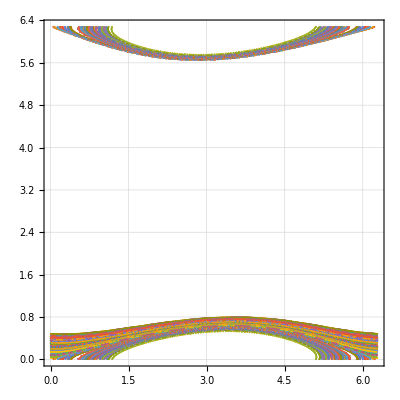

```mathematica
tb=Table[Transpose[{qLis[[;;,i]],pLis[[;;,i]]}],{i,1,sampleSize}];
ListPlot[tb[[;;,1;;]],{PlotTheme->"Detailed",AspectRatio->1}]
```

```mathematica
dataSet=Table[Abs[Conjugate[x].#]^2,{x,trueEigs}]&/@phiLis;
```

```mathematica
spec=Eigenvalues[Transpose[dataSet].dataSet];
Length[Select[Table[Total[spec[[1;;s]]]/Total[spec],{s,1,20}],#<0.99999&]]
```

9